```mathematica
ClearAll["Global`*"]
```

```mathematica
str:=2
K[n_] := If[ n==1,0,FullSimplify[MangoldtLambda[n]/Log[n]]]
K2[n_] := If[Floor[n^(1/str)]==n^(1/str),K[n^(1/str)],0]
K7[n_] := K2[n]-If[ Floor[Log[2,n]]==Log[2,n],n^(1/str) /Log[2,n],0]
P[n_,0]=1; 
P[n_, k_] := P[n,k] = Sum[ K7[j]P[Floor[n/j],k-1],{j,2,n}]
p[n_,k_]:=p[n,k]=P[n,k]-P[n-1,k]
En[n_] := En[n] = Sum[ 1/(k!) P[n,k],{k,0, Log[2,n]}]
En[n_,z_] := En[n,z] = Sum[ (z^k)/(k!) P[n,k],{k,0, Log[2,n]}]
En[n_,0]:=1
en[n_] := Sum[ 1/(k!) p[n,k],{k,0, Log[2,n]}]
en[n_,z_] := En[n,z]-En[n-1,z]
LAdd[n_] := Sum[ (2^(1/str))^k/k,{k,1,Log[str,n]}]
PP[n_,k_] := PP[n,k]=Sum[ 1/k-PP[Floor[n/j],k+1],{j,2,n}]
En2[n_,k_]:=En2[n,k]=Sum[(-1)^j Binomial[k,j]En[n,k-j],{j,0,k}]
Lin[n_]:=FullSimplify[Sum[ (-1)^(k+1)/k En2[n,k],{k,1,Log[2,n]}]]

b1[n_] := b1[n]=Floor[n^(1/str)]-Floor[(n^(1/str))/(2^(1/str))](2^(1/str))
bd[n_] := bd[n]=b1[n]-b1[n-1]

b1[n_] := b1[n]=Floor[n^(1/str)]-Floor[(n^(1/str))/(2^(1/str))](2^(1/str))
bd[n_] := bd[n]=b1[n]-b1[n-1]
s2[n_] := Sum[ bd[j]bd[k],{j,1,n},{k,1,Floor[n/j]}]
s2d[n_]:=s2[n]-s2[n-1]
s2[n_,k_]:=s2[n,k]=Sum[ bd[j]s2[Floor[n/j],k-1],{j,1,n}]
s2[n_,0]:=1
s2d[n_,k_]:=s2d[n,k]=FullSimplify[s2[n,k]-s2[n-1,k]]
D1[n_,k_]:=D1[n,k]=Sum[ D1[Floor[n/j],k-1],{j,1,n}];D1[n_,0]:=1
E1[n_,k_]:=E1[n,k]=Sum[ (-1)^(j+1)E1[Floor[n/j],k-1],{j,1,n}];E1[n_,0]:=1
S22[n_,k_]:=S22[n,k]=Sum[(-1)^j Binomial[k,j]s2[n,k-j],{j,0,k}]
LinS2[n_]:=FullSimplify[Sum[ (-1)^(k+1)/k S22[n,k],{k,1,Log[2,n]}]]


d2[n_,k_]:=d2[n,k]=Sum[d2[j,k-1] d2[n/j,1],{j,Divisors[n]}];d2[n_,1]:=1;d2[1,1]:=0;d2[n_,0]:=0;d2[1,0]:=1

t1[n_,a_] := Sum[ 1, {j,1,n},{k,1,Floor[n/j]}]
t2[n_,a_] := Sum[  ((2^(1/a))),{j,1,n},{k,1,Floor[ n/(j (2^(1/a)))]}]
t3[n_,a_]:=Sum[ 2^(1/a)2^(1/a),{j,1,n/(2^(1/a))},{k,1,n/(2^(1/a)2^(1/a) j )}]
ta[n_,a_]:=t1[n^(1/a),a]- 2t2[n^(1/a),a]+t3[n^(1/a),a]


t1[n_,a_] := t1[n,a]=Sum[ 1, {j,1,n},{k,1,Floor[n/j]}]
t2[n_,a_] := t2[n,a]=Sum[  a,{j,1,n},{k,1,Floor[ n/(j a)]}]
t3[n_,a_]:=t3[n,a]=Sum[ a a,{j,1,n/a},{k,1,n/(a a j )}]
ta[n_,a_]:=ta[n,a]=t1[n,a]- 2t2[n,a]+t3[n,a]


t21[n_,a_] := t21[n,a]=Sum[ 1, {j,2,n},{k,2,Floor[n/j]}]
t22[n_,a_] := t22[n,a]=Sum[  a,{j,2,n},{k,1,Floor[ n/(j a)]}]
t23[n_,a_]:=t23[n,a]=Sum[ a a,{j,1,n/a},{k,1,n/(a a j )}]
t2a[n_,a_]:=t2a[n,a]=t21[n,a]- 2t22[n,a]+t23[n,a]
d1a[n_]:=d1a[n]=Sum[1,{j,1,n},{k,1,Floor[n/j]}]
d2a[n_]:=d2a[n]=Sum[1,{j,2,n},{k,2,Floor[n/j]}]


t31[n_,a_] := t31[n,a]=Sum[ 1, {j,2,n},{k,2,Floor[n/j]},{m,2,Floor[n/(j k)]}]
t32[n_,a_] := t32[n,a]=Sum[  a,{j,2,n},{k,2,Floor[ n/j]},{m,1,Floor[ n/(j k a)]}]
t33[n_,a_]:=t33[n,a]=Sum[ a a,{j,2,n},{k,1,Floor[n/(a j )]},{m,1,Floor[ n/(j k a a)]}]
t34[n_,a_]:=t34[n,a]=Sum[ a a a,{j,1,n/a},{k,1,Floor[n/(a a j )]},{m,1,Floor[n/(a a a j k )]}]
t3a[n_,a_]:=t3a[n,a]=t31[n,a]- 3t32[n,a]+3t33[n,a]-t34[n,a]
d31a[n_]:=d31a[n]=Sum[1,{j,1,n},{k,1,Floor[n/j]},{m,1,Floor[n/(j k)]}]
d32a[n_]:=d32a[n]=Sum[1,{j,2,n},{k,2,Floor[n/j]},{m,2,Floor[n/(j k)]}]


t31[n_,a_] := t31[n,a]=Sum[ 1, {j,2,n},{k,2,Floor[n/j]},{m,2,Floor[n/(j k)]}]
t32[n_,a_] := t32[n,a]=Sum[  a,{j,2,n},{k,2,Floor[ n/j]},{m,1,Floor[ n/(j k a)]}]
t33[n_,a_]:=t33[n,a]=Sum[ a a,{j,2,n},{k,1,Floor[n/(a j )]},{m,1,Floor[ n/(j k a a)]}]
t34[n_,a_]:=t34[n,a]=Sum[ a a a,{j,1,n/a},{k,1,Floor[n/(a a j )]},{m,1,Floor[n/(a a a j k )]}]
t3a[n_,a_]:=t3a[n,a]=t31[n,a]- 3t32[n,a]+3t33[n,a]-t34[n,a]
t21[n_,a_] := t21[n,a]=Sum[ 1, {j,2,n},{k,2,Floor[n/j]}]
t22[n_,a_] := t22[n,a]=Sum[  a,{j,2,n},{k,1,Floor[ n/(j a)]}]
t23[n_,a_]:=t23[n,a]=Sum[ a a,{j,1,n/a},{k,1,n/(a a j )}]
t11[n_,a_] := t21[n,a]=Sum[ 1, {j,2,n}]
t12[n_,a_]:=t23[n,a]=Sum[ a ,{j,1,n/a}]
t1a[n_,a_]:=t11[n,a]-t12[n,a]
t2a[n_,a_]:=t2a[n,a]=t21[n,a]- 2t22[n,a]+t23[n,a]


tk[n_,k_, a_]:= tk[n,k,a]=Sum[ tk[n/j,k-1,a],{j,2,n}]-a Sum[ tk[n/(a j),k-1,a],{j,1,n/a}];tk[n_,0,a_]:=1
tk1[n_,k_, a_]:= tk1[n,k,a]=Sum[ tk1[n/j,k-1,a],{j,1,n}]-a Sum[ tk1[n/(a j),k-1,a],{j,1,n/a}];tk1[n_,0,a_]:=1
tk2[n_,k_,a_]:=tk2[n,k,a]=Sum[(-1)^j Binomial[k,j]tk1[n,k-j,a],{j,0,k}]


Lina[n_,a_]:=FullSimplify[Sum[ (-1)^(k+1)/k tk[n,k,a],{k,1,Log[2,n^2]}]]
LAdda[n_,a_] := Sum[ a^k/k,{k,1,Log[a,n]}]

LAdda2[n_,a_] := Sum[ (a^k-1)/k,{k,1,Log[a,n]}]
```

```mathematica
P[100^str,1]+LAdd[100^str]
```

428/15

```mathematica
P[100,1]+LAdd[100]
```

16/3

```mathematica
Lin[100]+LAdd[100]
```

16/3

```mathematica
Lin[10000]
```

44/3-(595471 √2)/45045

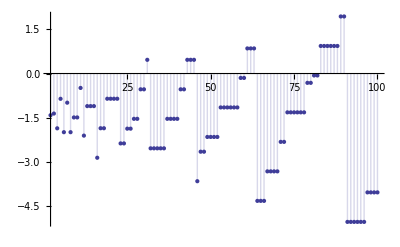

```mathematica
DiscretePlot[{Lin[n^str]},{n,2,100}]
```

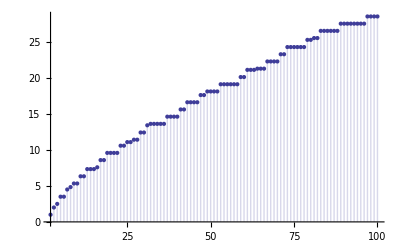

```mathematica
DiscretePlot[{P[n^str,1]+LAdd[n^str]},{n,2,100}]
```

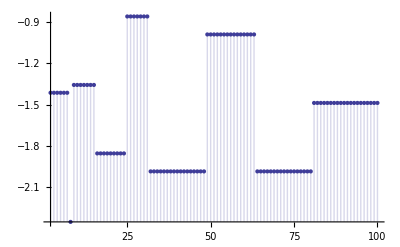

```mathematica
DiscretePlot[{P[n,1]},{n,2,100}]
```

```mathematica
Table[{n^(1/2),FullSimplify[en[n]], bd[n]},{n,2,50}]//TableForm
```

√2 | -2^(1/3) | -2^(1/3)
√3 | 0 | 0
2 | 0 | 0
√5 | 0 | 0
√6 | 0 | 0
√7 | 0 | 0
2 √2 | 1 | 1
3 | 0 | 0
√10 | 0 | 0
√11 | 0 | 0
2 √3 | 0 | 0
√13 | 0 | 0
√14 | 0 | 0
√15 | 0 | 0
4 | -2^(1/3) | -2^(1/3)
√17 | 0 | 0
3 √2 | 0 | 0
√19 | 0 | 0
2 √5 | 0 | 0
√21 | 0 | 0
√22 | 0 | 0
√23 | 0 | 0
2 √6 | 0 | 0
5 | 0 | 0
√26 | 0 | 0
3 √3 | 1 | 1
2 √7 | 0 | 0
√29 | 0 | 0
√30 | 0 | 0
√31 | 0 | 0
4 √2 | 0 | 0
√33 | 0 | 0
√34 | 0 | 0
√35 | 0 | 0
6 | 0 | 0
√37 | 0 | 0
√38 | 0 | 0
√39 | 0 | 0
2 √10 | 0 | 0
√41 | 0 | 0
√42 | 0 | 0
√43 | 0 | 0
2 √11 | 0 | 0
3 √5 | 0 | 0
√46 | 0 | 0
√47 | 0 | 0
4 √3 | 0 | 0
7 | 0 | 0
5 √2 | 0 | 0

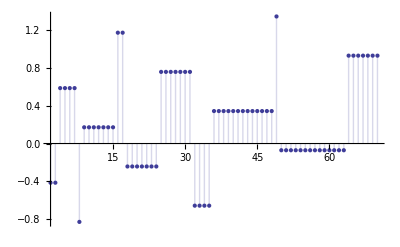

```mathematica
DiscretePlot[En[n],{n,2,70}]
```

```mathematica
Table[ {n^(1/2), FullSimplify[En[n]], Floor[n^(1/2)]-Floor[(n^(1/2))/(2^(1/2))](2^(1/2))},{n,1,100}]//TableForm
```

1 | 1 | 1
√2 | 1-√2 | 1-√2
√3 | 1-√2 | 1-√2
2 | 2-√2 | 2-√2
√5 | 2-√2 | 2-√2
√6 | 2-√2 | 2-√2
√7 | 2-√2 | 2-√2
2 √2 | 2-2 √2 | 2-2 √2
3 | 3-2 √2 | 3-2 √2
√10 | 3-2 √2 | 3-2 √2
√11 | 3-2 √2 | 3-2 √2
2 √3 | 3-2 √2 | 3-2 √2
√13 | 3-2 √2 | 3-2 √2
√14 | 3-2 √2 | 3-2 √2
√15 | 3-2 √2 | 3-2 √2
4 | 4-2 √2 | 4-2 √2
√17 | 4-2 √2 | 4-2 √2
3 √2 | 4-3 √2 | 4-3 √2
√19 | 4-3 √2 | 4-3 √2
2 √5 | 4-3 √2 | 4-3 √2
√21 | 4-3 √2 | 4-3 √2
√22 | 4-3 √2 | 4-3 √2
√23 | 4-3 √2 | 4-3 √2
2 √6 | 4-3 √2 | 4-3 √2
5 | 5-3 √2 | 5-3 √2
√26 | 5-3 √2 | 5-3 √2
3 √3 | 5-3 √2 | 5-3 √2
2 √7 | 5-3 √2 | 5-3 √2
√29 | 5-3 √2 | 5-3 √2
√30 | 5-3 √2 | 5-3 √2
√31 | 5-3 √2 | 5-3 √2
4 √2 | 5-4 √2 | 5-4 √2
√33 | 5-4 √2 | 5-4 √2
√34 | 5-4 √2 | 5-4 √2
√35 | 5-4 √2 | 5-4 √2
6 | 6-4 √2 | 6-4 √2
√37 | 6-4 √2 | 6-4 √2
√38 | 6-4 √2 | 6-4 √2
√39 | 6-4 √2 | 6-4 √2
2 √10 | 6-4 √2 | 6-4 √2
√41 | 6-4 √2 | 6-4 √2
√42 | 6-4 √2 | 6-4 √2
√43 | 6-4 √2 | 6-4 √2
2 √11 | 6-4 √2 | 6-4 √2
3 √5 | 6-4 √2 | 6-4 √2
√46 | 6-4 √2 | 6-4 √2
√47 | 6-4 √2 | 6-4 √2
4 √3 | 6-4 √2 | 6-4 √2
7 | 7-4 √2 | 7-4 √2
5 √2 | 7-5 √2 | 7-5 √2
√51 | 7-5 √2 | 7-5 √2
2 √13 | 7-5 √2 | 7-5 √2
√53 | 7-5 √2 | 7-5 √2
3 √6 | 7-5 √2 | 7-5 √2
√55 | 7-5 √2 | 7-5 √2
2 √14 | 7-5 √2 | 7-5 √2
√57 | 7-5 √2 | 7-5 √2
√58 | 7-5 √2 | 7-5 √2
√59 | 7-5 √2 | 7-5 √2
2 √15 | 7-5 √2 | 7-5 √2
√61 | 7-5 √2 | 7-5 √2
√62 | 7-5 √2 | 7-5 √2
3 √7 | 7-5 √2 | 7-5 √2
8 | 8-5 √2 | 8-5 √2
√65 | 8-5 √2 | 8-5 √2
√66 | 8-5 √2 | 8-5 √2
√67 | 8-5 √2 | 8-5 √2
2 √17 | 8-5 √2 | 8-5 √2
√69 | 8-5 √2 | 8-5 √2
√70 | 8-5 √2 | 8-5 √2
√71 | 8-5 √2 | 8-5 √2
6 √2 | 8-6 √2 | 8-6 √2
√73 | 8-6 √2 | 8-6 √2
√74 | 8-6 √2 | 8-6 √2
5 √3 | 8-6 √2 | 8-6 √2
2 √19 | 8-6 √2 | 8-6 √2
√77 | 8-6 √2 | 8-6 √2
√78 | 8-6 √2 | 8-6 √2
√79 | 8-6 √2 | 8-6 √2
4 √5 | 8-6 √2 | 8-6 √2
9 | 9-6 √2 | 9-6 √2
√82 | 9-6 √2 | 9-6 √2
√83 | 9-6 √2 | 9-6 √2
2 √21 | 9-6 √2 | 9-6 √2
√85 | 9-6 √2 | 9-6 √2
√86 | 9-6 √2 | 9-6 √2
√87 | 9-6 √2 | 9-6 √2
2 √22 | 9-6 √2 | 9-6 √2
√89 | 9-6 √2 | 9-6 √2
3 √10 | 9-6 √2 | 9-6 √2
√91 | 9-6 √2 | 9-6 √2
2 √23 | 9-6 √2 | 9-6 √2
√93 | 9-6 √2 | 9-6 √2
√94 | 9-6 √2 | 9-6 √2
√95 | 9-6 √2 | 9-6 √2
4 √6 | 9-6 √2 | 9-6 √2
√97 | 9-6 √2 | 9-6 √2
7 √2 | 9-7 √2 | 9-7 √2
3 √11 | 9-7 √2 | 9-7 √2
10 | 10-7 √2 | 10-7 √2

```mathematica
Table[ {n^(1/2), FullSimplify[en[n,1]]},{n,1,100}]//TableForm
```

1 | 1
√2 | -√2
√3 | 0
2 | 1
√5 | 0
√6 | 0
√7 | 0
2 √2 | -√2
3 | 1
√10 | 0
√11 | 0
2 √3 | 0
√13 | 0
√14 | 0
√15 | 0
4 | 1
√17 | 0
3 √2 | -√2
√19 | 0
2 √5 | 0
√21 | 0
√22 | 0
√23 | 0
2 √6 | 0
5 | 1
√26 | 0
3 √3 | 0
2 √7 | 0
√29 | 0
√30 | 0
√31 | 0
4 √2 | -√2
√33 | 0
√34 | 0
√35 | 0
6 | 1
√37 | 0
√38 | 0
√39 | 0
2 √10 | 0
√41 | 0
√42 | 0
√43 | 0
2 √11 | 0
3 √5 | 0
√46 | 0
√47 | 0
4 √3 | 0
7 | 1
5 √2 | -√2
√51 | 0
2 √13 | 0
√53 | 0
3 √6 | 0
√55 | 0
2 √14 | 0
√57 | 0
√58 | 0
√59 | 0
2 √15 | 0
√61 | 0
√62 | 0
3 √7 | 0
8 | 1
√65 | 0
√66 | 0
√67 | 0
2 √17 | 0
√69 | 0
√70 | 0
√71 | 0
6 √2 | -√2
√73 | 0
√74 | 0
5 √3 | 0
2 √19 | 0
√77 | 0
√78 | 0
√79 | 0
4 √5 | 0
9 | 1
√82 | 0
√83 | 0
2 √21 | 0
√85 | 0
√86 | 0
√87 | 0
2 √22 | 0
√89 | 0
3 √10 | 0
√91 | 0
2 √23 | 0
√93 | 0
√94 | 0
√95 | 0
4 √6 | 0
√97 | 0
7 √2 | -√2
3 √11 | 0
10 | 1

```mathematica
N[10/(2^(1/2))]
```

7.07107

```mathematica
Table[ {n, FullSimplify[En[n^2]] , (n-Floor[n/(2^(1/2))](2^(1/2)))},{n,1,30}]//TableForm
```

1 | 1 | 1
2 | 2-√2 | 2-√2
3 | 3-2 √2 | 3-2 √2
4 | 4-2 √2 | 4-2 √2
5 | 5-3 √2 | 5-3 √2
6 | 6-4 √2 | 6-4 √2
7 | 7-4 √2 | 7-4 √2
8 | 8-5 √2 | 8-5 √2
9 | 9-6 √2 | 9-6 √2
10 | 10-7 √2 | 10-7 √2
11 | 11-7 √2 | 11-7 √2
12 | 12-8 √2 | 12-8 √2
13 | 13-9 √2 | 13-9 √2
14 | 14-9 √2 | 14-9 √2
15 | 15-10 √2 | 15-10 √2
16 | 16-11 √2 | 16-11 √2
17 | 17-12 √2 | 17-12 √2
18 | 18-12 √2 | 18-12 √2
19 | 19-13 √2 | 19-13 √2
20 | 20-14 √2 | 20-14 √2
21 | 21-14 √2 | 21-14 √2
22 | 22-15 √2 | 22-15 √2
23 | 23-16 √2 | 23-16 √2
24 | 24-16 √2 | 24-16 √2
25 | 25-17 √2 | 25-17 √2
26 | 26-18 √2 | 26-18 √2
27 | 27-19 √2 | 27-19 √2
28 | 28-19 √2 | 28-19 √2
29 | 29-20 √2 | 29-20 √2
30 | 30-21 √2 | 30-21 √2

```mathematica
Table[ {n, N[(n-Floor[n/(2^(1/1155))](2^(1/1155)))]},{n,1,100}]//TableForm
```

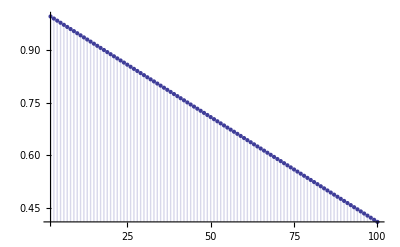

```mathematica
DiscretePlot[(n-Floor[n/(2^(1/117))](2^(1/117))),{n,2,100}]
```

```mathematica
Table[ {n^(1/2), FullSimplify[en[n,2]], s2d[n],s2d[n,2]},{n,1,100}]//TableForm
```

1 | 1 | 1 | 1
√2 | -2 √2 | -2 √2 | -2 √2
√3 | 0 | 0 | 0
2 | 4 | 4 | 4
√5 | 0 | 0 | 0
√6 | 0 | 0 | 0
√7 | 0 | 0 | 0
2 √2 | -4 √2 | -4 √2 | -4 √2
3 | 2 | 2 | 2
√10 | 0 | 0 | 0
√11 | 0 | 0 | 0
2 √3 | 0 | 0 | 0
√13 | 0 | 0 | 0
√14 | 0 | 0 | 0
√15 | 0 | 0 | 0
4 | 7 | 7 | 7
√17 | 0 | 0 | 0
3 √2 | -4 √2 | -4 √2 | -4 √2
√19 | 0 | 0 | 0
2 √5 | 0 | 0 | 0
√21 | 0 | 0 | 0
√22 | 0 | 0 | 0
√23 | 0 | 0 | 0
2 √6 | 0 | 0 | 0
5 | 2 | 2 | 2
√26 | 0 | 0 | 0
3 √3 | 0 | 0 | 0
2 √7 | 0 | 0 | 0
√29 | 0 | 0 | 0
√30 | 0 | 0 | 0
√31 | 0 | 0 | 0
4 √2 | -6 √2 | -6 √2 | -6 √2
√33 | 0 | 0 | 0
√34 | 0 | 0 | 0
√35 | 0 | 0 | 0
6 | 8 | 8 | 8
√37 | 0 | 0 | 0
√38 | 0 | 0 | 0
√39 | 0 | 0 | 0
2 √10 | 0 | 0 | 0
√41 | 0 | 0 | 0
√42 | 0 | 0 | 0
√43 | 0 | 0 | 0
2 √11 | 0 | 0 | 0
3 √5 | 0 | 0 | 0
√46 | 0 | 0 | 0
√47 | 0 | 0 | 0
4 √3 | 0 | 0 | 0
7 | 2 | 2 | 2
5 √2 | -4 √2 | -4 √2 | -4 √2
√51 | 0 | 0 | 0
2 √13 | 0 | 0 | 0
√53 | 0 | 0 | 0
3 √6 | 0 | 0 | 0
√55 | 0 | 0 | 0
2 √14 | 0 | 0 | 0
√57 | 0 | 0 | 0
√58 | 0 | 0 | 0
√59 | 0 | 0 | 0
2 √15 | 0 | 0 | 0
√61 | 0 | 0 | 0
√62 | 0 | 0 | 0
3 √7 | 0 | 0 | 0
8 | 10 | 10 | 10
√65 | 0 | 0 | 0
√66 | 0 | 0 | 0
√67 | 0 | 0 | 0
2 √17 | 0 | 0 | 0
√69 | 0 | 0 | 0
√70 | 0 | 0 | 0
√71 | 0 | 0 | 0
6 √2 | -8 √2 | -8 √2 | -8 √2
√73 | 0 | 0 | 0
√74 | 0 | 0 | 0
5 √3 | 0 | 0 | 0
2 √19 | 0 | 0 | 0
√77 | 0 | 0 | 0
√78 | 0 | 0 | 0
√79 | 0 | 0 | 0
4 √5 | 0 | 0 | 0
9 | 3 | 3 | 3
√82 | 0 | 0 | 0
√83 | 0 | 0 | 0
2 √21 | 0 | 0 | 0
√85 | 0 | 0 | 0
√86 | 0 | 0 | 0
√87 | 0 | 0 | 0
2 √22 | 0 | 0 | 0
√89 | 0 | 0 | 0
3 √10 | 0 | 0 | 0
√91 | 0 | 0 | 0
2 √23 | 0 | 0 | 0
√93 | 0 | 0 | 0
√94 | 0 | 0 | 0
√95 | 0 | 0 | 0
4 √6 | 0 | 0 | 0
√97 | 0 | 0 | 0
7 √2 | -4 √2 | -4 √2 | -4 √2
3 √11 | 0 | 0 | 0
10 | 8 | 8 | 8

```mathematica
Table[ {n^(1/2), FullSimplify[en[n,4]], s2d[n,4]},{n,1,100}]//TableForm
```

1 | 1 | 1
√2 | -4 √2 | -4 √2
√3 | 0 | 0
2 | 16 | 16
√5 | 0 | 0
√6 | 0 | 0
√7 | 0 | 0
2 √2 | -24 √2 | -24 √2
3 | 4 | 4
√10 | 0 | 0
√11 | 0 | 0
2 √3 | 0 | 0
√13 | 0 | 0
√14 | 0 | 0
√15 | 0 | 0
4 | 62 | 62
√17 | 0 | 0
3 √2 | -16 √2 | -16 √2
√19 | 0 | 0
2 √5 | 0 | 0
√21 | 0 | 0
√22 | 0 | 0
√23 | 0 | 0
2 √6 | 0 | 0
5 | 4 | 4
√26 | 0 | 0
3 √3 | 0 | 0
2 √7 | 0 | 0
√29 | 0 | 0
√30 | 0 | 0
√31 | 0 | 0
4 √2 | -72 √2 | -72 √2
√33 | 0 | 0
√34 | 0 | 0
√35 | 0 | 0
6 | 64 | 64
√37 | 0 | 0
√38 | 0 | 0
√39 | 0 | 0
2 √10 | 0 | 0
√41 | 0 | 0
√42 | 0 | 0
√43 | 0 | 0
2 √11 | 0 | 0
3 √5 | 0 | 0
√46 | 0 | 0
√47 | 0 | 0
4 √3 | 0 | 0
7 | 4 | 4
5 √2 | -16 √2 | -16 √2
√51 | 0 | 0
2 √13 | 0 | 0
√53 | 0 | 0
3 √6 | 0 | 0
√55 | 0 | 0
2 √14 | 0 | 0
√57 | 0 | 0
√58 | 0 | 0
√59 | 0 | 0
2 √15 | 0 | 0
√61 | 0 | 0
√62 | 0 | 0
3 √7 | 0 | 0
8 | 156 | 156
√65 | 0 | 0
√66 | 0 | 0
√67 | 0 | 0
2 √17 | 0 | 0
√69 | 0 | 0
√70 | 0 | 0
√71 | 0 | 0
6 √2 | -96 √2 | -96 √2
√73 | 0 | 0
√74 | 0 | 0
5 √3 | 0 | 0
2 √19 | 0 | 0
√77 | 0 | 0
√78 | 0 | 0
√79 | 0 | 0
4 √5 | 0 | 0
9 | 10 | 10
√82 | 0 | 0
√83 | 0 | 0
2 √21 | 0 | 0
√85 | 0 | 0
√86 | 0 | 0
√87 | 0 | 0
2 √22 | 0 | 0
√89 | 0 | 0
3 √10 | 0 | 0
√91 | 0 | 0
2 √23 | 0 | 0
√93 | 0 | 0
√94 | 0 | 0
√95 | 0 | 0
4 √6 | 0 | 0
√97 | 0 | 0
7 √2 | -16 √2 | -16 √2
3 √11 | 0 | 0
10 | 64 | 64

```mathematica
Table[ {n^(1/2), FullSimplify[s2[n,2]],ta[n,2]},{n,1,100}]//TableForm
```

1 | s2[1,2] | 1
√2 | s2[2,2] | 1-2 √2
√3 | s2[3,2] | 1-2 √2
2 | s2[4,2] | 5-2 √2
√5 | s2[5,2] | 5-2 √2
√6 | s2[6,2] | 5-2 √2
√7 | s2[7,2] | 5-2 √2
2 √2 | s2[8,2] | 5-6 √2
3 | s2[9,2] | 7-6 √2
√10 | s2[10,2] | 7-6 √2
√11 | s2[11,2] | 7-6 √2
2 √3 | s2[12,2] | 7-6 √2
√13 | s2[13,2] | 7-6 √2
√14 | s2[14,2] | 7-6 √2
√15 | s2[15,2] | 7-6 √2
4 | s2[16,2] | 14-6 √2
√17 | s2[17,2] | 14-6 √2
3 √2 | s2[18,2] | 14-10 √2
√19 | s2[19,2] | 14-10 √2
2 √5 | s2[20,2] | 14-10 √2
√21 | s2[21,2] | 14-10 √2
√22 | s2[22,2] | 14-10 √2
√23 | s2[23,2] | 14-10 √2
2 √6 | s2[24,2] | 14-10 √2
5 | s2[25,2] | 16-10 √2
√26 | s2[26,2] | 16-10 √2
3 √3 | s2[27,2] | 16-10 √2
2 √7 | s2[28,2] | 16-10 √2
√29 | s2[29,2] | 16-10 √2
√30 | s2[30,2] | 16-10 √2
√31 | s2[31,2] | 16-10 √2
4 √2 | s2[32,2] | 16-16 √2
√33 | s2[33,2] | 16-16 √2
√34 | s2[34,2] | 16-16 √2
√35 | s2[35,2] | 16-16 √2
6 | s2[36,2] | 24-16 √2
√37 | s2[37,2] | 24-16 √2
√38 | s2[38,2] | 24-16 √2
√39 | s2[39,2] | 24-16 √2
2 √10 | s2[40,2] | 24-16 √2
√41 | s2[41,2] | 24-16 √2
√42 | s2[42,2] | 24-16 √2
√43 | s2[43,2] | 24-16 √2
2 √11 | s2[44,2] | 24-16 √2
3 √5 | s2[45,2] | 24-16 √2
√46 | s2[46,2] | 24-16 √2
√47 | s2[47,2] | 24-16 √2
4 √3 | s2[48,2] | 24-16 √2
7 | s2[49,2] | 26-16 √2
5 √2 | s2[50,2] | 26-20 √2
√51 | s2[51,2] | 26-20 √2
2 √13 | s2[52,2] | 26-20 √2
√53 | s2[53,2] | 26-20 √2
3 √6 | s2[54,2] | 26-20 √2
√55 | s2[55,2] | 26-20 √2
2 √14 | s2[56,2] | 26-20 √2
√57 | s2[57,2] | 26-20 √2
√58 | s2[58,2] | 26-20 √2
√59 | s2[59,2] | 26-20 √2
2 √15 | s2[60,2] | 26-20 √2
√61 | s2[61,2] | 26-20 √2
√62 | s2[62,2] | 26-20 √2
3 √7 | s2[63,2] | 26-20 √2
8 | s2[64,2] | 36-20 √2
√65 | s2[65,2] | 36-20 √2
√66 | s2[66,2] | 36-20 √2
√67 | s2[67,2] | 36-20 √2
2 √17 | s2[68,2] | 36-20 √2
√69 | s2[69,2] | 36-20 √2
√70 | s2[70,2] | 36-20 √2
√71 | s2[71,2] | 36-20 √2
6 √2 | s2[72,2] | 36-28 √2
√73 | s2[73,2] | 36-28 √2
√74 | s2[74,2] | 36-28 √2
5 √3 | s2[75,2] | 36-28 √2
2 √19 | s2[76,2] | 36-28 √2
√77 | s2[77,2] | 36-28 √2
√78 | s2[78,2] | 36-28 √2
√79 | s2[79,2] | 36-28 √2
4 √5 | s2[80,2] | 36-28 √2
9 | s2[81,2] | 39-28 √2
√82 | s2[82,2] | 39-28 √2
√83 | s2[83,2] | 39-28 √2
2 √21 | s2[84,2] | 39-28 √2
√85 | s2[85,2] | 39-28 √2
√86 | s2[86,2] | 39-28 √2
√87 | s2[87,2] | 39-28 √2
2 √22 | s2[88,2] | 39-28 √2
√89 | s2[89,2] | 39-28 √2
3 √10 | s2[90,2] | 39-28 √2
√91 | s2[91,2] | 39-28 √2
2 √23 | s2[92,2] | 39-28 √2
√93 | s2[93,2] | 39-28 √2
√94 | s2[94,2] | 39-28 √2
√95 | s2[95,2] | 39-28 √2
4 √6 | s2[96,2] | 39-28 √2
√97 | s2[97,2] | 39-28 √2
7 √2 | s2[98,2] | 39-32 √2
3 √11 | s2[99,2] | 39-32 √2
10 | s2[100,2] | 47-32 √2

1 | 1 | 1
√2 | 1-2 √2 | 1-2 √2
√3 | 1-2 √2 | 1-2 √2
2 | 5-2 √2 | 5-2 √2
√5 | 5-2 √2 | 5-2 √2
√6 | 5-2 √2 | 5-2 √2
√7 | 5-2 √2 | 5-2 √2
2 √2 | 5-6 √2 | 5-6 √2
3 | 7-6 √2 | 7-6 √2
√10 | 7-6 √2 | 7-6 √2
√11 | 7-6 √2 | 7-6 √2
2 √3 | 7-6 √2 | 7-6 √2
√13 | 7-6 √2 | 7-6 √2
√14 | 7-6 √2 | 7-6 √2
√15 | 7-6 √2 | 7-6 √2
4 | 14-6 √2 | 14-6 √2
√17 | 14-6 √2 | 14-6 √2
3 √2 | 14-10 √2 | 14-10 √2
√19 | 14-10 √2 | 14-10 √2
2 √5 | 14-10 √2 | 14-10 √2
√21 | 14-10 √2 | 14-10 √2
√22 | 14-10 √2 | 14-10 √2
√23 | 14-10 √2 | 14-10 √2
2 √6 | 14-10 √2 | 14-10 √2
5 | 16-10 √2 | 16-10 √2
√26 | 16-10 √2 | 16-10 √2
3 √3 | 16-10 √2 | 16-10 √2
2 √7 | 16-10 √2 | 16-10 √2
√29 | 16-10 √2 | 16-10 √2
√30 | 16-10 √2 | 16-10 √2
√31 | 16-10 √2 | 16-10 √2
4 √2 | -16 (-1+√2) | 16-16 √2
√33 | -16 (-1+√2) | 16-16 √2
√34 | -16 (-1+√2) | 16-16 √2
√35 | -16 (-1+√2) | 16-16 √2
6 | 24-16 √2 | 24-16 √2
√37 | 24-16 √2 | 24-16 √2
√38 | 24-16 √2 | 24-16 √2
√39 | 24-16 √2 | 24-16 √2
2 √10 | 24-16 √2 | 24-16 √2
√41 | 24-16 √2 | 24-16 √2
√42 | 24-16 √2 | 24-16 √2
√43 | 24-16 √2 | 24-16 √2
2 √11 | 24-16 √2 | 24-16 √2
3 √5 | 24-16 √2 | 24-16 √2
√46 | 24-16 √2 | 24-16 √2
√47 | 24-16 √2 | 24-16 √2
4 √3 | 24-16 √2 | 24-16 √2
7 | 26-16 √2 | 26-16 √2
5 √2 | 26-20 √2 | 26-20 √2
√51 | 26-20 √2 | 26-20 √2
2 √13 | 26-20 √2 | 26-20 √2
√53 | 26-20 √2 | 26-20 √2
3 √6 | 26-20 √2 | 26-20 √2
√55 | 26-20 √2 | 26-20 √2
2 √14 | 26-20 √2 | 26-20 √2
√57 | 26-20 √2 | 26-20 √2
√58 | 26-20 √2 | 26-20 √2
√59 | 26-20 √2 | 26-20 √2
2 √15 | 26-20 √2 | 26-20 √2
√61 | 26-20 √2 | 26-20 √2
√62 | 26-20 √2 | 26-20 √2
3 √7 | 26-20 √2 | 26-20 √2
8 | 36-20 √2 | 36-20 √2
√65 | 36-20 √2 | 36-20 √2
√66 | 36-20 √2 | 36-20 √2
√67 | 36-20 √2 | 36-20 √2
2 √17 | 36-20 √2 | 36-20 √2
√69 | 36-20 √2 | 36-20 √2
√70 | 36-20 √2 | 36-20 √2
√71 | 36-20 √2 | 36-20 √2
6 √2 | 36-28 √2 | 36-28 √2
√73 | 36-28 √2 | 36-28 √2
√74 | 36-28 √2 | 36-28 √2
5 √3 | 36-28 √2 | 36-28 √2
2 √19 | 36-28 √2 | 36-28 √2
√77 | 36-28 √2 | 36-28 √2
√78 | 36-28 √2 | 36-28 √2
√79 | 36-28 √2 | 36-28 √2
4 √5 | 36-28 √2 | 36-28 √2
9 | 39-28 √2 | 39-28 √2
√82 | 39-28 √2 | 39-28 √2
√83 | 39-28 √2 | 39-28 √2
2 √21 | 39-28 √2 | 39-28 √2
√85 | 39-28 √2 | 39-28 √2
√86 | 39-28 √2 | 39-28 √2
√87 | 39-28 √2 | 39-28 √2
2 √22 | 39-28 √2 | 39-28 √2
√89 | 39-28 √2 | 39-28 √2
3 √10 | 39-28 √2 | 39-28 √2
√91 | 39-28 √2 | 39-28 √2
2 √23 | 39-28 √2 | 39-28 √2
√93 | 39-28 √2 | 39-28 √2
√94 | 39-28 √2 | 39-28 √2
√95 | 39-28 √2 | 39-28 √2
4 √6 | 39-28 √2 | 39-28 √2
√97 | 39-28 √2 | 39-28 √2
7 √2 | 39-32 √2 | 39-32 √2
3 √11 | 39-32 √2 | 39-32 √2
10 | 47-32 √2 | 47-32 √2

```mathematica
FullSimplify[bd[n]]
```

-Floor[√(-1+n)]+√2 Floor[(√(-1+n))/(√2)]+Floor[√n]-√2 Floor[(√n)/(√2)]

```mathematica
Table[ {n^(1/2), FullSimplify[s2[n,2]],ta[n^(1/2),2^(1/2)]},{n,1,100}]//TableForm
```

1 | s2[1,2] | 1
√2 | s2[2,2] | 1-2 √2
√3 | s2[3,2] | 1-2 √2
2 | s2[4,2] | 5-2 √2
√5 | s2[5,2] | 5-2 √2
√6 | s2[6,2] | 5-2 √2
√7 | s2[7,2] | 5-2 √2
2 √2 | s2[8,2] | 5-6 √2
3 | s2[9,2] | 7-6 √2
√10 | s2[10,2] | 7-6 √2
√11 | s2[11,2] | 7-6 √2
2 √3 | s2[12,2] | 7-6 √2
√13 | s2[13,2] | 7-6 √2
√14 | s2[14,2] | 7-6 √2
√15 | s2[15,2] | 7-6 √2
4 | s2[16,2] | 14-6 √2
√17 | s2[17,2] | 14-6 √2
3 √2 | s2[18,2] | 14-10 √2
√19 | s2[19,2] | 14-10 √2
2 √5 | s2[20,2] | 14-10 √2
√21 | s2[21,2] | 14-10 √2
√22 | s2[22,2] | 14-10 √2
√23 | s2[23,2] | 14-10 √2
2 √6 | s2[24,2] | 14-10 √2
5 | s2[25,2] | 16-10 √2
√26 | s2[26,2] | 16-10 √2
3 √3 | s2[27,2] | 16-10 √2
2 √7 | s2[28,2] | 16-10 √2
√29 | s2[29,2] | 16-10 √2
√30 | s2[30,2] | 16-10 √2
√31 | s2[31,2] | 16-10 √2
4 √2 | s2[32,2] | 16-16 √2
√33 | s2[33,2] | 16-16 √2
√34 | s2[34,2] | 16-16 √2
√35 | s2[35,2] | 16-16 √2
6 | s2[36,2] | 24-16 √2
√37 | s2[37,2] | 24-16 √2
√38 | s2[38,2] | 24-16 √2
√39 | s2[39,2] | 24-16 √2
2 √10 | s2[40,2] | 24-16 √2
√41 | s2[41,2] | 24-16 √2
√42 | s2[42,2] | 24-16 √2
√43 | s2[43,2] | 24-16 √2
2 √11 | s2[44,2] | 24-16 √2
3 √5 | s2[45,2] | 24-16 √2
√46 | s2[46,2] | 24-16 √2
√47 | s2[47,2] | 24-16 √2
4 √3 | s2[48,2] | 24-16 √2
7 | s2[49,2] | 26-16 √2
5 √2 | s2[50,2] | 26-20 √2
√51 | s2[51,2] | 26-20 √2
2 √13 | s2[52,2] | 26-20 √2
√53 | s2[53,2] | 26-20 √2
3 √6 | s2[54,2] | 26-20 √2
√55 | s2[55,2] | 26-20 √2
2 √14 | s2[56,2] | 26-20 √2
√57 | s2[57,2] | 26-20 √2
√58 | s2[58,2] | 26-20 √2
√59 | s2[59,2] | 26-20 √2
2 √15 | s2[60,2] | 26-20 √2
√61 | s2[61,2] | 26-20 √2
√62 | s2[62,2] | 26-20 √2
3 √7 | s2[63,2] | 26-20 √2
8 | s2[64,2] | 36-20 √2
√65 | s2[65,2] | 36-20 √2
√66 | s2[66,2] | 36-20 √2
√67 | s2[67,2] | 36-20 √2
2 √17 | s2[68,2] | 36-20 √2
√69 | s2[69,2] | 36-20 √2
√70 | s2[70,2] | 36-20 √2
√71 | s2[71,2] | 36-20 √2
6 √2 | s2[72,2] | 36-28 √2
√73 | s2[73,2] | 36-28 √2
√74 | s2[74,2] | 36-28 √2
5 √3 | s2[75,2] | 36-28 √2
2 √19 | s2[76,2] | 36-28 √2
√77 | s2[77,2] | 36-28 √2
√78 | s2[78,2] | 36-28 √2
√79 | s2[79,2] | 36-28 √2
4 √5 | s2[80,2] | 36-28 √2
9 | s2[81,2] | 39-28 √2
√82 | s2[82,2] | 39-28 √2
√83 | s2[83,2] | 39-28 √2
2 √21 | s2[84,2] | 39-28 √2
√85 | s2[85,2] | 39-28 √2
√86 | s2[86,2] | 39-28 √2
√87 | s2[87,2] | 39-28 √2
2 √22 | s2[88,2] | 39-28 √2
√89 | s2[89,2] | 39-28 √2
3 √10 | s2[90,2] | 39-28 √2
√91 | s2[91,2] | 39-28 √2
2 √23 | s2[92,2] | 39-28 √2
√93 | s2[93,2] | 39-28 √2
√94 | s2[94,2] | 39-28 √2
√95 | s2[95,2] | 39-28 √2
4 √6 | s2[96,2] | 39-28 √2
√97 | s2[97,2] | 39-28 √2
7 √2 | s2[98,2] | 39-32 √2
3 √11 | s2[99,2] | 39-32 √2
10 | s2[100,2] | 47-32 √2

```mathematica
Table[ {n, ta[n,2^(1/2)]},{n,1,100}]//TableForm
```

1 | 1
2 | 5-2 √2
3 | 7-6 √2
4 | 14-6 √2
5 | 16-10 √2
6 | 24-16 √2
7 | 26-16 √2
8 | 36-20 √2
9 | 39-28 √2
10 | 47-32 √2
11 | 49-32 √2
12 | 63-40 √2
13 | 65-46 √2
14 | 73-46 √2
15 | 77-54 √2
16 | 90-58 √2
17 | 92-70 √2
18 | 104-70 √2
19 | 106-74 √2
20 | 120-82 √2
21 | 124-82 √2
22 | 132-90 √2
23 | 134-100 √2
24 | 154-100 √2
25 | 157-104 √2
26 | 165-116 √2
27 | 169-120 √2
28 | 183-120 √2
29 | 185-132 √2
30 | 201-140 √2
31 | 203-140 √2
32 | 219-148 √2
33 | 223-152 √2
34 | 231-168 √2
35 | 235-168 √2
36 | 256-174 √2
37 | 258-182 √2
38 | 266-182 √2
39 | 270-190 √2
40 | 290-202 √2
41 | 292-202 √2
42 | 308-206 √2
43 | 310-222 √2
44 | 324-226 √2
45 | 330-226 √2
46 | 338-238 √2
47 | 340-246 √2
48 | 366-246 √2
49 | 369-254 √2
50 | 381-262 √2
51 | 385-280 √2
52 | 399-280 √2
53 | 401-284 √2
54 | 417-292 √2
55 | 421-292 √2
56 | 441-300 √2
57 | 445-316 √2
58 | 453-320 √2
59 | 455-320 √2
60 | 483-336 √2
61 | 485-340 √2
62 | 493-340 √2
63 | 499-352 √2
64 | 518-364 √2
65 | 522-364 √2
66 | 538-372 √2
67 | 540-376 √2
68 | 554-396 √2
69 | 558-396 √2
70 | 574-402 √2
71 | 576-414 √2
72 | 606-414 √2
73 | 608-422 √2
74 | 616-434 √2
75 | 622-438 √2
76 | 636-438 √2
77 | 640-454 √2
78 | 656-462 √2
79 | 658-462 √2
80 | 684-478 √2
81 | 689-486 √2
82 | 697-486 √2
83 | 699-494 √2
84 | 727-498 √2
85 | 731-522 √2
86 | 739-522 √2
87 | 743-526 √2
88 | 763-534 √2
89 | 765-534 √2
90 | 789-546 √2
91 | 793-560 √2
92 | 807-568 √2
93 | 811-568 √2
94 | 819-584 √2
95 | 823-588 √2
96 | 855-588 √2
97 | 857-600 √2
98 | 869-608 √2
99 | 875-624 √2
100 | 896-624 √2

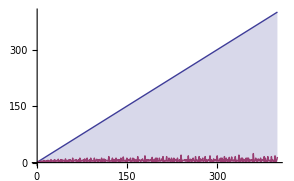

```mathematica
DiscretePlot[ {n, ta[n,1.00000001]},{n,1,400}]//TableForm
```

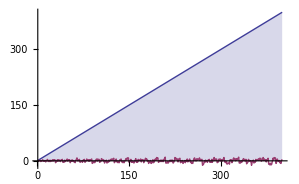

```mathematica
DiscretePlot[ {n, ta[n,2]},{n,1,400}]//TableForm
```

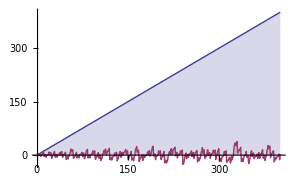

```mathematica
DiscretePlot[ {n, ta[n,3]},{n,1,400}]//TableForm
```

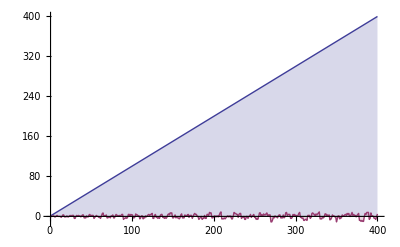

```mathematica
DiscretePlot[ {n, t2a[n,2]},{n,1,400}]//TableForm
```

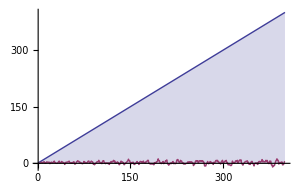

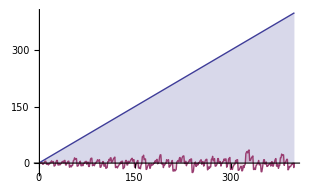

```mathematica
DiscretePlot[ {n,t2a[n,3]},{n,1,400}]//TableForm
```

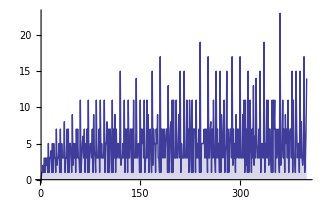

```mathematica
DiscretePlot[ {t2a[n,1.00000001]},{n,1,400}]//TableForm
```

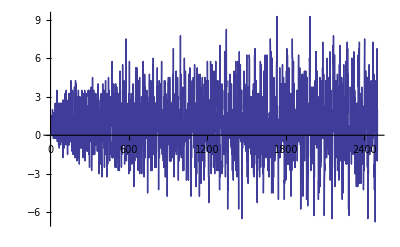

```mathematica
DiscretePlot[ {t2a[n,.5]-n/2},{n,1,2500}]//TableForm
```

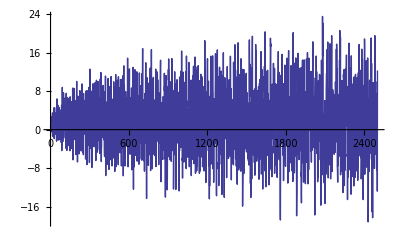

```mathematica
DiscretePlot[ {t2a[n,.6]-n*.4},{n,1,2500}]//TableForm
```

```mathematica
N[1750/2500]
```

0.7

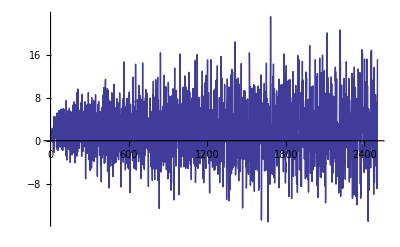

```mathematica
DiscretePlot[ {t2a[n,.4]-n*.7},{n,1,2500}]//TableForm
```

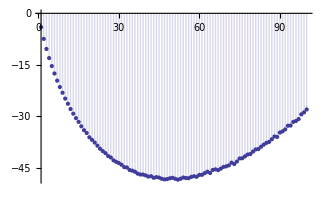

```mathematica
DiscretePlot[ {d2a[n]-t2a[n,1/32]},{n,1,100}]//TableForm
```

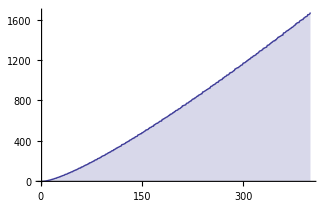

```mathematica
DiscretePlot[ {d2a[n]},{n,1,400}]//TableForm
```

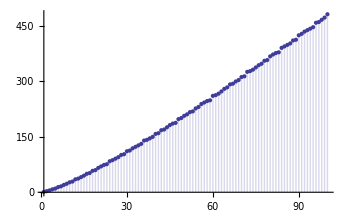

```mathematica
DiscretePlot[ {d1a[n]-ta[n,1]},{n,1,100}]//TableForm
```

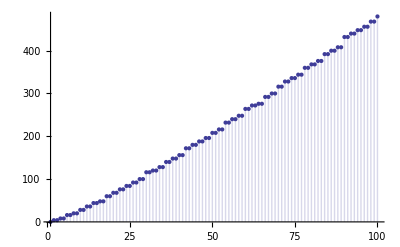

```mathematica
DiscretePlot[ {d1a[n]-ta[n,2]},{n,1,100}]//TableForm
```

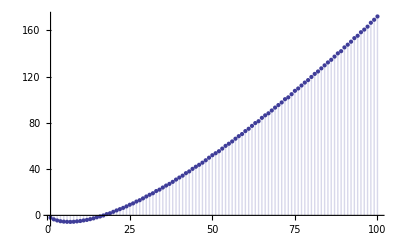

```mathematica
DiscretePlot[ {d1a[n]-ta[n,1/32]},{n,1,100}]//TableForm
```

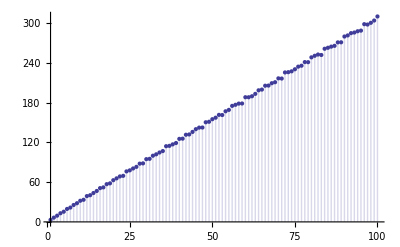

```mathematica
DiscretePlot[ {ta[n,1/32]},{n,1,100}]//TableForm
```

```mathematica
bs[n_]:=n Log[n]+n(2 EulerGamma-1)
```

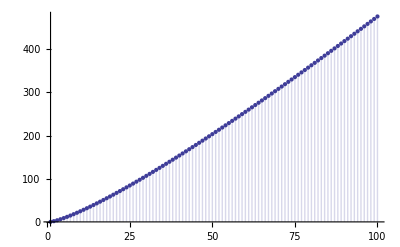

```mathematica
DiscretePlot[ bs[n],{n,1,100}]
```

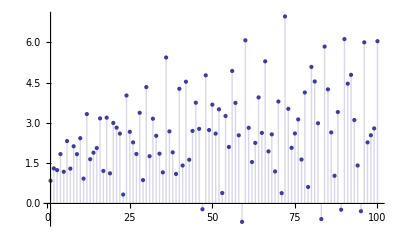

```mathematica
DiscretePlot[ {d1a[n]-ta[n,1]-bs[n]},{n,1,100}]//TableForm
```

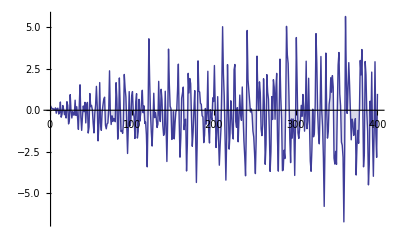

```mathematica
DiscretePlot[ {d1a[n]-EulerGamma ta[n,1+.0000000001]-bs[n]},{n,1,400}]//TableForm
```

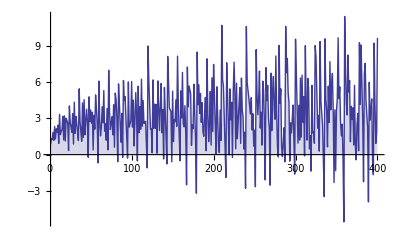

```mathematica
DiscretePlot[ {d1a[n]-bs[n]},{n,1,400}]//TableForm
```

```mathematica
DiscretePlot[ {ta[n,1/64]},{n,1,40}]//TableForm
DiscretePlot[ {ta[n,1/128]},{n,1,40}]//TableForm
DiscretePlot[ {ta[n,1/256]},{n,1,40}]//TableForm
```

```mathematica
Animate[DiscretePlot[ {600,-100,ta[n,Sin[s]*49+50]},{n,1,100}],{s,0,2Pi}]
```

```mathematica
Sum[ .5^k/k,{k,1,Log[.5,10]}]
```

0

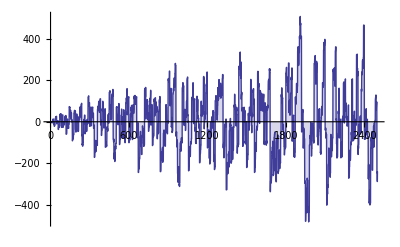

```mathematica
DiscretePlot[ {t3a[n,3]},{n,1,2500}]
```

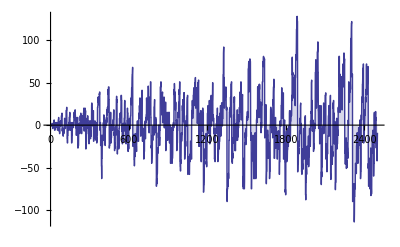

```mathematica
DiscretePlot[ {t3a[n,2]},{n,1,2500}]
```

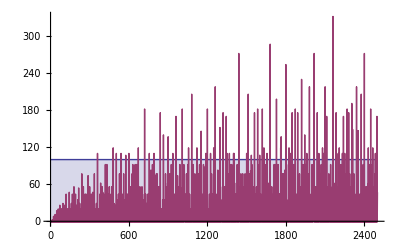

```mathematica
DiscretePlot[ {100,t3a[n,1.0000000001]},{n,1,2500}]
```

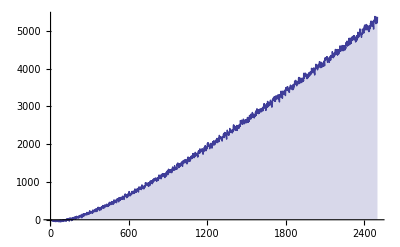

```mathematica
DiscretePlot[ {t3a[n,.4]},{n,1,2500}]
```

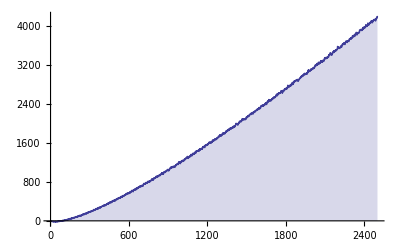

```mathematica
DiscretePlot[ {t3a[n,.5]},{n,1,2500}]
```

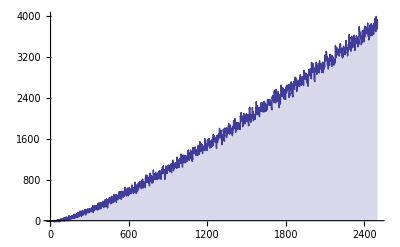

```mathematica
DiscretePlot[ {t3a[n,.6]},{n,1,2500}]
```

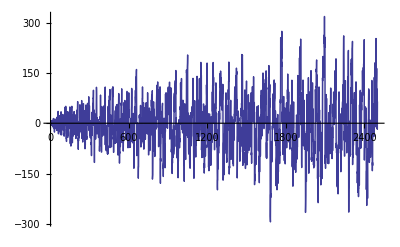

```mathematica
DiscretePlot[ {t3a[n,1.5]},{n,1,2500}]
```

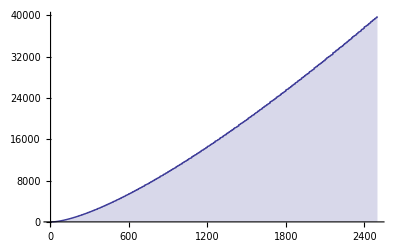

```mathematica
DiscretePlot[ {t3a[n,999]},{n,1,2500}]
```

```mathematica
DiscretePlot[ {d32a[n]},{n,1,2500}]
```

-Graphics-

```mathematica
Sum[ 1.000001^k/k,{k,1,Log[ 1.000001,100]}]-Sum[ 1.000001^k/k,{k,1,Log[ 1.000001,1.45136923488338105]}]
```

30.1262-2.46016×10^-10 ⅈ

```mathematica
N[LogIntegral[100]]
```

30.1261

```mathematica
Table[ {n,t3a[n,1.0000000001],d32a[n]-d32a[n-1]},{n,1,100}]//TableForm
```

1 | 0 | 0
2 | -1. | 0
3 | -1. | 0
4 | -1. | 0
5 | -1. | 0
6 | -1. | 0
7 | -1. | 0
8 | -2.09999×10^-9 | 1
9 | -1. | 0
10 | -1. | 0
11 | -1. | 0
12 | 2. | 3
13 | -1. | 0
14 | -1. | 0
15 | -1. | 0
16 | 2. | 3
17 | -1. | 0
18 | 2. | 3
19 | -1. | 0
20 | 2. | 3
21 | -1. | 0
22 | -1. | 0
23 | -1. | 0
24 | 8. | 9
25 | -1. | 0
26 | -1. | 0
27 | -7.7998×10^-9 | 1
28 | 2. | 3
29 | -1. | 0
30 | 5. | 6
31 | -1. | 0
32 | 5. | 6
33 | -1. | 0
34 | -1. | 0
35 | -1. | 0
36 | 11. | 12
37 | -1. | 0
38 | -1. | 0
39 | -1. | 0
40 | 8. | 9
41 | -1. | 0
42 | 5. | 6
43 | -1. | 0
44 | 2. | 3
45 | 2. | 3
46 | -1. | 0
47 | -1. | 0
48 | 17. | 18
49 | -1. | 0
50 | 2. | 3
51 | -1. | 0
52 | 2. | 3
53 | -1. | 0
54 | 8. | 9
55 | -1. | 0
56 | 8. | 9
57 | -1. | 0
58 | -1. | 0
59 | -1. | 0
60 | 20. | 21
61 | -1. | 0
62 | -1. | 0
63 | 2. | 3
64 | 9. | 10
65 | -1. | 0
66 | 5. | 6
67 | -1. | 0
68 | 2. | 3
69 | -1. | 0
70 | 5. | 6
71 | -1. | 0
72 | 26. | 27
73 | -1. | 0
74 | -1. | 0
75 | 2. | 3
76 | 2. | 3
77 | -1. | 0
78 | 5. | 6
79 | -1. | 0
80 | 17. | 18
81 | 2. | 3
82 | -1. | 0
83 | -1. | 0
84 | 20. | 21
85 | -1. | 0
86 | -1. | 0
87 | -1. | 0
88 | 8. | 9
89 | -1. | 0
90 | 20. | 21
91 | -1. | 0
92 | 2. | 3
93 | -1. | 0
94 | -1. | 0
95 | -1. | 0
96 | 29. | 30
97 | -1. | 0
98 | 2. | 3
99 | 2. | 3
100 | 11. | 12

```mathematica
Table[ {n,t2a[n,1.0000000001],d2a[n]-d2a[n-1]},{n,1,100}]//TableForm
```

1 | 0 | 0
2 | 1. | 0
3 | 1. | 0
4 | 2. | 1
5 | 1. | 0
6 | 3. | 2
7 | 1. | 0
8 | 3. | 2
9 | 2. | 1
10 | 3. | 2
11 | 1. | 0
12 | 5. | 4
13 | 1. | 0
14 | 3. | 2
15 | 3. | 2
16 | 4. | 3
17 | 1. | 0
18 | 5. | 4
19 | 1. | 0
20 | 5. | 4
21 | 3. | 2
22 | 3. | 2
23 | 1. | 0
24 | 7. | 6
25 | 2. | 1
26 | 3. | 2
27 | 3. | 2
28 | 5. | 4
29 | 1. | 0
30 | 7. | 6
31 | 1. | 0
32 | 5. | 4
33 | 3. | 2
34 | 3. | 2
35 | 3. | 2
36 | 8. | 7
37 | 1. | 0
38 | 3. | 2
39 | 3. | 2
40 | 7. | 6
41 | 1. | 0
42 | 7. | 6
43 | 1. | 0
44 | 5. | 4
45 | 5. | 4
46 | 3. | 2
47 | 1. | 0
48 | 9. | 8
49 | 2. | 1
50 | 5. | 4
51 | 3. | 2
52 | 5. | 4
53 | 1. | 0
54 | 7. | 6
55 | 3. | 2
56 | 7. | 6
57 | 3. | 2
58 | 3. | 2
59 | 1. | 0
60 | 11. | 10
61 | 1. | 0
62 | 3. | 2
63 | 5. | 4
64 | 6. | 5
65 | 3. | 2
66 | 7. | 6
67 | 1. | 0
68 | 5. | 4
69 | 3. | 2
70 | 7. | 6
71 | 1. | 0
72 | 11. | 10
73 | 1. | 0
74 | 3. | 2
75 | 5. | 4
76 | 5. | 4
77 | 3. | 2
78 | 7. | 6
79 | 1. | 0
80 | 9. | 8
81 | 4. | 3
82 | 3. | 2
83 | 1. | 0
84 | 11. | 10
85 | 3. | 2
86 | 3. | 2
87 | 3. | 2
88 | 7. | 6
89 | 1. | 0
90 | 11. | 10
91 | 3. | 2
92 | 5. | 4
93 | 3. | 2
94 | 3. | 2
95 | 3. | 2
96 | 11. | 10
97 | 1. | 0
98 | 5. | 4
99 | 5. | 4
100 | 8. | 7

```mathematica
t2a[100,2^(1/2)]
```

499-346 √2

```mathematica
FullSimplify[tk1[100,3,2^(1/2)]]
```

4855-3321 √2

```mathematica
FullSimplify[En[100^2,3]]
```

4855-3321 √2

```mathematica
FullSimplify[ta[100,2^(1/2)]]
```

896-624 √2

```mathematica
FullSimplify[Lina[100,2^(1/2)]]+LAdda[100,2^(1/2)]
```

428/15

$Aborted

```mathematica
Lin[10000]+LAdd[10000]
```

428/15

```mathematica
Table[ {n, a=FullSimplify[En2[10000,n]], b=FullSimplify[tk2[100,n,2^(1/2)]],a-b},{n,1,12}]//TableForm
```

$Aborted

```mathematica
FullSimplify[tk[100,1,2^(1/2)]]
```

99-69 √2

```mathematica
Table[{n,FullSimplify[En2[n^2,3]],a=FullSimplify[tk[n,3,2^(1/2)]],b=FullSimplify[tk2[n,3,2^(1/2)]],a-b},{n,1,30}]//TableForm
```

1 | 0 | 0 | 0 | 0
2 | 0 | 0 | 0 | 0
3 | -2 √2 | -2 √2 | -2 √2 | 0
4 | 6-2 √2 | 6-2 √2 | 6-2 √2 | 0
5 | 6-2 √2 | 6-2 √2 | 6-2 √2 | 0
6 | 12-11 √2 | 12-11 √2 | 12-11 √2 | 0
7 | 12-11 √2 | 12-11 √2 | 12-11 √2 | 0
8 | 31-11 √2 | 31-11 √2 | 31-11 √2 | 0
9 | 31-23 √2 | 31-23 √2 | 31-23 √2 | 0
10 | 37-23 √2 | 37-23 √2 | 37-23 √2 | 0
11 | 37-23 √2 | 37-23 √2 | 37-23 √2 | 0
12 | 70-44 √2 | 70-44 √2 | 70-44 √2 | 0
13 | 70-47 √2 | 70-47 √2 | 70-47 √2 | 0
14 | 76-47 √2 | 76-47 √2 | 76-47 √2 | 0
15 | 76-59 √2 | 76-59 √2 | 76-59 √2 | 0
16 | 115-59 √2 | 115-59 √2 | 115-59 √2 | 0
17 | 115-98 √2 | 115-98 √2 | 115-98 √2 | 0
18 | 136-98 √2 | 136-98 √2 | 136-98 √2 | 0
19 | 136-98 √2 | 136-98 √2 | 136-98 √2 | 0
20 | 169-110 √2 | 169-110 √2 | 169-110 √2 | 0
21 | 169-110 √2 | 169-110 √2 | 169-110 √2 | 0
22 | 175-116 √2 | 175-116 √2 | 175-116 √2 | 0
23 | 175-154 √2 | 175-154 √2 | 175-154 √2 | 0
24 | 256-154 √2 | 256-154 √2 | 256-154 √2 | 0
25 | 256-154 √2 | 256-154 √2 | 256-154 √2 | 0
26 | 262-187 √2 | 262-187 √2 | 262-187 √2 | 0
27 | 263-187 √2 | 263-187 √2 | 263-187 √2 | 0
28 | 296-187 √2 | 296-187 √2 | 296-187 √2 | 0
29 | 296-226 √2 | 296-226 √2 | 296-226 √2 | 0
30 | 332-232 √2 | 332-232 √2 | 332-232 √2 | 0

```mathematica
Table[{k,FullSimplify[tk[100,k,2^(1/2)]]},{k,1,15}]//TableForm
```

1 | 99-70 √2
2 | 697-484 √2
3 | 2466-1659 √2
4 | 5780-3652 √2
5 | 9971-5844 √2
6 | 13393-7376 √2
7 | 14140-7743 √2
8 | 11464-6832 √2
9 | 6864-4984 √2
10 | 48 (59-60 √2)
11 | 704-1264 √2
12 | 64-384 √2
13 | -64 √2
14 | 0
15 | 0

```mathematica
Table[{k,FullSimplify[tk[100,k,2]]},{k,1,Log[2,100^2]}]//TableForm
```

1 | -1
2 | 3
3 | -4
4 | -8
5 | 9
6 | -5
7 | 0
8 | 0
9 | 0
10 | 0
11 | 0
12 | 0
13 | 0

```mathematica
Table[{k,FullSimplify[tk[100,k,2^(1/3)]]},{k,1,Log[2^(1/3),100]+1}]//TableForm
```

1 | 99-79 2^(1/3)
2 | 283-558 2^(1/3)+267 2^(2/3)
3 | 3 (-268-402 2^(1/3)+483 2^(2/3))
4 | -5288+436 2^(1/3)+2802 2^(2/3)
5 | -9849+6340 2^(1/3)+468 2^(2/3)
6 | -3673+10878 2^(1/3)-6915 2^(2/3)
7 | 15386+4133 2^(1/3)-10878 2^(2/3)
8 | -4 (-6692+2727 2^(1/3)+811 2^(2/3))
9 | 4 (2632-4041 2^(1/3)+1971 2^(2/3))
10 | 8 (-2105-549 2^(1/3)+1080 2^(2/3))
11 | 16 (-1320+539 2^(1/3)+49 2^(2/3))
12 | -16 (181-528 2^(1/3)+234 2^(2/3))
13 | 16 (533+25 2^(1/3)-117 2^(2/3))
14 | 16 (273-224 2^(1/3)+29 2^(2/3))
15 | 16 (-62-105 2^(1/3)+30 2^(2/3))
16 | 32 (-32+17 2^(1/3))
17 | -32 2^(1/3) (-17+2^(1/3))
18 | 64
19 | -64 2^(1/3)
20 | 0

```mathematica
Table[{k,FullSimplify[tk[100,k,2^(1/4)]]},{k,1,Log[2^(1/4),100]+1}]//TableForm
```

1 | 99-84 2^(1/4)
2 | 283-614 2^(1/4)+312 √2
3 | 324-1401 2^(1/4)+1731 √2-684 2^(3/4)
4 | -4 (-670+365 2^(1/4)-843 √2+836 2^(3/4))
5 | 11841-4344 2^(1/4)+3030 √2-6060 2^(3/4)
6 | 21307-15894 2^(1/4)+5392 √2-5200 2^(3/4)
7 | 18760-25627 2^(1/4)+16667 √2-6631 2^(3/4)
8 | -4 (-4904+4760 2^(1/4)-6237 √2+4368 2^(3/4))
9 | 4 (11394-3955 2^(1/4)+4494 √2-5994 2^(3/4))
10 | 4 (15930-8456 2^(1/4)+3641 √2-3660 2^(3/4))
11 | 40920-40040 2^(1/4)+29128 √2-9596 2^(3/4)
12 | -4 (-6085+4840 2^(1/4)-8844 √2+4644 2^(3/4))
13 | 4 (10894-2771 2^(1/4)+4862 √2-4524 2^(3/4))
14 | 43680-21392 2^(1/4)+11348 √2-5824 2^(3/4)
15 | -56 (-260+315 2^(1/4)-360 √2+58 2^(3/4))
16 | 16 (441-280 2^(1/4)+1140 √2-408 2^(3/4))
17 | -16 (-901+205 2^(1/4)-340 √2+204 2^(3/4))
18 | 16 (459-378 2^(1/4)+208 √2)
19 | -48 2^(1/4) (57-133 2^(1/4)+13 √2)
20 | 32 (41+95 √2-20 2^(3/4))
21 | 64 (21-11 2^(1/4))
22 | 32 2^(1/4) (-22+23 2^(1/4))
23 | -32 √2 (-23+2^(1/4))
24 | 64
25 | -64 2^(1/4)
26 | 64 √2
27 | 0

```mathematica
Lina[n_,a_]:=FullSimplify[Sum[ (-1)^(k+1)/k tk[n,k,a],{k,1,Log[a,n]}]]
LAdda[n_,a_] := Sum[ a^k/k,{k,1,Log[a,n]}]
```

```mathematica
Lina[100,2^(1/3)]+LAdda[100,2^(1/3)]
```

428/15

```mathematica
Lina[100,2^(1/4)]+LAdda[100,2^(1/4)]
```

428/15

```mathematica
Lina[100,2^(1/5)]+LAdda[100,2^(1/5)]
```

428/15

```mathematica
Lina[100,2^(1/6)]+LAdda[100,2^(1/6)]
```

428/15

```mathematica
Lina[100,2^(1/7)]+LAdda[100,2^(1/7)]
```

428/15

```mathematica
N[LAdda[100,2^(1/7)]]
```

32.3667

```mathematica
N[Lina[100,2^(1/7)]]
```

-3.83334

```mathematica
Lina[100,2^(1/8)]+LAdda[100,2^(1/8)]
```

428/15

```mathematica
N[2^(1/8)]
```

1.09051

```mathematica
Table[{k,FullSimplify[tk[100,k,2^(1/8)]]},{k,1,Log[2^(1/8),100]+1}]//TableForm
```

$Aborted

```mathematica
Lina[100,1.1]+LAdda[100,1.1]
```

28.5333

```mathematica
Lina[100,1.05]+LAdda[100,1.05]
```

28.5333

```mathematica
$RecursionLimit=1000000
```

1000000

```mathematica
Lina[100,1.01]+LAdda[100,1.01]
```

$RecursionLimit::reclim: Recursion depth of 256 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$Aborted

```mathematica
N[2^(1/4)]
```

1.18921

```mathematica
Table[{k,N[ (-1)^(k+1)/k tk[100,k,1.000000001]]},{k,1,60}]//TableForm
```

1 | -9.9×10^-8
2 | -4.
3 | 3.66667
4 | -1.75
5 | -0.2
6 | -0.166667
7 | -0.142857
8 | -0.125
9 | -0.111111
10 | -0.1
11 | -0.0909092
12 | -0.0833334
13 | -0.0769232
14 | -0.0714287
15 | -0.0666668
16 | -0.0625001
17 | -0.0588236
18 | -0.0555557
19 | -0.0526317
20 | -0.0500001
21 | -0.0476191
22 | -0.0454546
23 | -0.0434784
24 | -0.0416668
25 | -0.0400001
26 | -0.0384616
27 | -0.0370371
28 | -0.0357144
29 | -0.0344829
30 | -0.0333334
31 | -0.0322582
32 | -0.0312501
33 | -0.0303031
34 | -0.0294119
35 | -0.0285715
36 | -0.0277779
37 | -0.0270271
38 | -0.0263159
39 | -0.0256411
40 | -0.0250001
41 | -0.0243903
42 | -0.0238096
43 | -0.0232559
44 | -0.0227274
45 | -0.0222223
46 | -0.0217392
47 | -0.0212767
48 | -0.0208334
49 | -0.0204083
50 | -0.0200001
51 | -0.0196079
52 | -0.0192309
53 | -0.018868
54 | -0.0185186
55 | -0.0181819
56 | -0.0178572
57 | -0.017544
58 | -0.0172415
59 | -0.0169493
60 | -0.0166668

```mathematica
Table[{k,N[  (-1)^(k+1)/k tk[100,k,1.000000001] ]- (1.000000001^k)/k},{k,1,60}]//TableForm
```

1 | -1.
2 | -4.5
3 | 3.33333
4 | -2.
5 | -0.4
6 | -0.333333
7 | -0.285714
8 | -0.25
9 | -0.222222
10 | -0.2
11 | -0.181818
12 | -0.166667
13 | -0.153846
14 | -0.142857
15 | -0.133333
16 | -0.125
17 | -0.117647
18 | -0.111111
19 | -0.105263
20 | -0.1
21 | -0.0952382
22 | -0.0909092
23 | -0.0869566
24 | -0.0833334
25 | -0.0800001
26 | -0.0769232
27 | -0.0740742
28 | -0.0714287
29 | -0.0689656
30 | -0.0666668
31 | -0.0645162
32 | -0.0625001
33 | -0.0606062
34 | -0.0588236
35 | -0.057143
36 | -0.0555557
37 | -0.0540542
38 | -0.0526317
39 | -0.0512822
40 | -0.0500001
41 | -0.0487806
42 | -0.0476191
43 | -0.0465117
44 | -0.0454546
45 | -0.0444445
46 | -0.0434784
47 | -0.0425533
48 | -0.0416668
49 | -0.0408164
50 | -0.0400001
51 | -0.0392158
52 | -0.0384616
53 | -0.0377359
54 | -0.0370371
55 | -0.0363637
56 | -0.0357144
57 | -0.0350878
58 | -0.0344829
59 | -0.0338984
60 | -0.0333334

```mathematica
Table[{k,N[ (-1)^(k+1)/k tk[10,k,1/2]]},{k,1,14}]//TableForm
```

1 | -1.
2 | -0.75
3 | -0.916667
4 | -1.15625
5 | -1.675
6 | -1.21875
7 | 1.23884
8 | 4.10986
9 | 1.26584
10 | -12.8259
11 | -31.5639
12 | -23.5638
13 | 48.3149
14 | 163.709

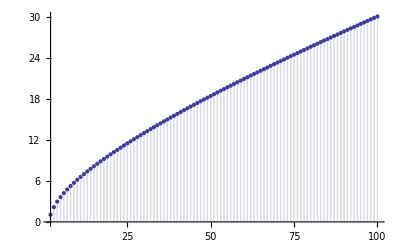

```mathematica
DiscretePlot[LAdda[n,1.001]-LAdda[1.45,1.001],{n,2,100}]
```

```mathematica
Table[{k,N[ (-1)^(k+1)/k tk[100,k,2^(1/8)]]},{k,1,Log[2^(1/8),100]+1}]//TableForm
```

1 | -0.236204
2 | -5.39838
3 | 24.1214
4 | -62.4699
5 | -42.037
6 | 548.661
7 | -1325.21
8 | 1603.75
9 | -280.997
10 | -3187.62
11 | 6504.76
12 | -5112.89
13 | -792.106
14 | 6150.91
15 | -9740.41
16 | 10301.8
17 | -2080.73
18 | -10566.4
19 | 12884.3
20 | -4667.05
21 | -1368.73
22 | 5085.55
23 | -10691.7
24 | 9816.99
25 | -304.917
26 | -5405.04
27 | 2863.91
28 | -107.805
29 | -159.677
30 | 2208.43
31 | -4094.19
32 | 1900.08
33 | 562.25
34 | -537.039
35 | 10.8383
36 | -8.99013
37 | -9.87027
38 | 513.882
39 | -474.455
40 | -6.11174
41 | 28.2526
42 | -4.06444
43 | -4.40933
44 | -4.78449
45 | -5.1926
46 | 48.1808
47 | -1.24869
48 | -1.33333
49 | -1.42434
50 | -1.52219
51 | -1.62741
52 | -1.74057
53 | -1.86229
54 | 0.

```mathematica
N[LAdda2[100,1.000001]]
N[LAdda[100,1.000001]]
```

28.0218-2.46016×10^-10 ⅈ

43.9417-2.46016×10^-10 ⅈ

```mathematica
N[LogIntegral[100]]
```

30.1261

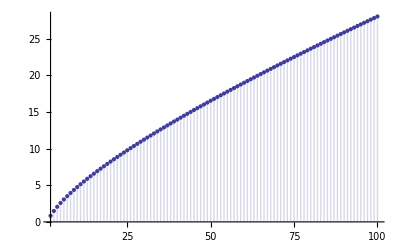

Power::infy: Infinite expression 1/0 encountered.

```mathematica
DiscretePlot[ LAdda2[n,1.0001],{n,2,100}]
```